```mathematica
rcap = {Sin[#1] Cos[#2], Sin[#1] Sin[#2], Cos[#1]} & ;
phicap = {-Sin[#2], Cos[#2], 0} & ;
thetacap = {Cos[#1] Cos[#2], Cos[#1] Sin[#2], -Sin[#1]} & ;
origin = {0,0,0} ;


asz = 1 ;
toff = 0.1 ;
axes = Graphics3D[{
Red,Arrow[Tube[{{0,0,0},{asz,0,0}}] , 0.05],
Blue,Arrow[Tube[{{0,0,0},{0,asz,0}}] , 0.05],
Darker[Green, .8],Arrow[Tube[{{0,0,0},{0,0,asz}}] , 0.05],
Text[ "e_1",  {asz + toff,0,0} ],
Text[ "e_2",  {0,asz + toff,0} ],
Text[ "e_3",  {0,0,asz + toff} ]
}] ;

f = (1 + Cos[#1])(-Cos[#2] thetacap[#1, #2] + Sin[#2]phicap[#1, #2]) & ;

Manipulate[ 
With[ 
{
rcapPt=  rcap[thetaP, phiP],
fPt = f[thetaP, phiP],

thetacapPt = thetacap[thetaP, phiP],
phicapPt = phicap[thetaP, phiP],
vecOff = 1.1 
},
Show[
ParametricPlot3D[ 
{Norm[f[t, p]] rcap[t, p]},
 {t, 0, Pi}, 
{p, 0, 2 Pi}, 
AxesLabel -> {x, y, z},
PlotStyle->Directive[Opacity[0.7]],
PlotRange->range{{-1.5,1.5},{-1.5,1.5}, {-0.4,2.5}}
]
,axes
,
With[{
fDir = fPt/Norm[fPt],
hDir = Cross[rcapPt, fPt/Norm[fPt]],
sPt = Norm[fPt] rcapPt
},
Graphics3D[{
Orange,Arrow[Tube[{sPt, sPt + rcapPt}] , 0.05],
Purple,Arrow[Tube[{sPt, sPt + fDir}] , 0.05],
Blue,Arrow[Tube[{sPt, sPt + hDir}] , 0.05],
Text[ "k̂",sPt + rcapPt vecOff],
Text[ "Ê", sPt + fDir vecOff],
Text[ "Ĥ", sPt + hDir vecOff]
}] ] (* With Graphics3D *) 
] (* Show *)
] (* With *)
,{{thetaP, 0.5 (*Pi/8 // N*), "θ"}, 0, 2 Pi, Appearance->"Labeled"}
,{{phiP, 1(*Pi/8 // N*), "ϕ"}, 0, 2 Pi, Appearance->"Labeled"}
, {{range, 1}, 0.1, 5}
,Initialization:> {
}
(*,
SaveDefinitions->True*)
]
```

```mathematica
sample1 = -Graphics3D- ;
sample2 = -Graphics3D- ;
```

```mathematica
<<peeters` ;
peeters`setGitDir[ "figures\\ece1229" ]
```

C:\Users\Peeter\cygwin_home\physicsplay\figures\ece1229

```mathematica
peeters`exportForLatex["electricAndMagneticDipoleSuperpositionFig1", sample1]
peeters`exportForLatex["electricAndMagneticDipoleSuperpositionFig2", sample2]
```

{C:\Users\Peeter\cygwin_home\physicsplay\figures\ece1229/electricAndMagneticDipoleSuperpositionFig1.eps,C:\Users\Peeter\cygwin_home\physicsplay\figures\ece1229/electricAndMagneticDipoleSuperpositionFig1pn.png}

{C:\Users\Peeter\cygwin_home\physicsplay\figures\ece1229/electricAndMagneticDipoleSuperpositionFig2.eps,C:\Users\Peeter\cygwin_home\physicsplay\figures\ece1229/electricAndMagneticDipoleSuperpositionFig2pn.png}

```mathematica
fZY = f[#1,Pi/2] & ;
fZYt = fZY[#1] . thetacap[#1, Pi/2] & ;
fZYp = fZY[#1] . phicap[#1, Pi/2] & ;
```

```mathematica
fZYt[θ] // Simplify
fZYp[θ] // Simplify
```

0

1+Cos[θ]

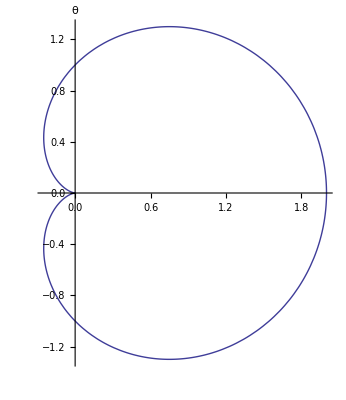

```mathematica
pp = PolarPlot[ fZYp[t], {t, 0, 2 Pi }, AxesLabel->θ]
```

```mathematica
peeters`exportForLatex["electricAndMagneticDipoleSuperpositionFig3", pp]
```

{C:\Users\Peeter\cygwin_home\physicsplay\figures\ece1229/electricAndMagneticDipoleSuperpositionFig3.eps,C:\Users\Peeter\cygwin_home\physicsplay\figures\ece1229/electricAndMagneticDipoleSuperpositionFig3pn.png}